```mathematica
Clear["Global`*"];
```

System model

### Model equations (x→ω[rad/s], y→i[A])

```mathematica
MomentEquation = θ x'[t] +b x[t] == k y[t]-TL;
KirchoffEquation = L y'[t]+R y[t] ==V-k x[t];
```

### Model parameters (estimated with MATLAB)

```mathematica
θ=0.012099670934420;
b=0.019715497097366;
k=0.824871094407238;
R=7.975905973570620;
L=0.165503732732700;
```

### State-space model

```mathematica
StateMatirx=({{-b/θ, k/θ}, {-k/L, -R/L}});InputMatrix=({{-TL/θ}, {V/L}});
```

```mathematica
({{a1, b1}, {a2, b2}})=StateMatirx;({{c1}, {c2}})=InputMatrix;
```

```mathematica
f[t_,x_,y_]:=({{a1, b1}, {a2, b2}}).{x,y}+({{c1}, {c2}})//Flatten
```

```mathematica
f[t,x,y]
```

{-82.6469 TL-1.62942 x+68.173 y,6.04216 V-4.984 x-48.1917 y}

### Stationary points

```mathematica
sp={x,y}/.Solve[f[t,x,y]=={0,0},{x,y}]
```

{{-9.52164 TL+0.984731 V,0.984731 TL+0.0235364 V}}

```mathematica
V=12;TL=0;
```

```mathematica
Options[myStreamPlot]=Options[StreamPlot];
myStreamPlot[g_,{x_,x0_,x1_},{y_,y0_,y1_},opts:OptionsPattern[]]:=With[{a=OptionValue[AspectRatio]},Show[StreamPlot[{1/(x1-x0),a/(y1-y0)} (g/.{x->x0+u (x1-x0),y->y0+v/a (y1-y0)}),{u,0,1},{v,0,a},opts]/.Arrow[pts_]:>Arrow[({x0,y0}+{x1-x0,(y1-y0)/a} #)&/@pts],PlotRange->{{x0,x1},{y0,y1}}]]
```

```mathematica
show1=myStreamPlot[{-82.6468 TL-1.6294 x+68.1730 y,6.0421 V-4.9840x-48.1916 y},{x,-10,20},{y,-1,2}];
```

```mathematica
show2=ListPlot[sp,PlotStyle->{PointSize[0.03],Black}];
```

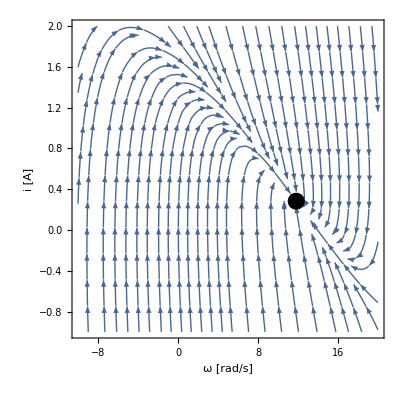

```mathematica
Show[show1,show2,FrameLabel->{"ω [rad/s]","i [A]"},PlotTheme->"Monochrome",Frame->True,AspectRatio->1,LabelStyle->FontSize->16,Axes->True]
```

Analytic solution

```mathematica
Clear[V,TL];
```

#### Homogenous solution

```mathematica
charEq=CharacteristicPolynomial[({{a1, b1}, {a2, b2}}),λ]==0;
λ1=λ/.Solve[charEq,λ][[1]];
λ2=λ/.Solve[charEq,λ][[2]];
```

```mathematica
xh[t_]:=C1 b1 E^(λ1 t)+C2 b1 E^(λ2 t)
yh[t_]:=C1 (λ1-a1) E^(λ1 t)+C2 (λ2-a1) E^(λ2 t)
```

#### Particular solution

```mathematica
peq1=a1 X0+b1 Y0+c1==0;
peq2=a2 X0+b2 Y0+c2==0;
```

```mathematica
particaluarSol=Solve[{peq1,peq2},{X0,Y0}];
```

```mathematica
xp[t_]:=X0/.particaluarSol[[1]]
```

```mathematica
yp[t_]:=Y0/.particaluarSol[[1]]
```

#### General solution

```mathematica
x[t_]:=xh[t]+xp[t]
```

```mathematica
y[t_]:=yh[t]+yp[t]
```

#### Initial conditions solution

```mathematica
constants=Solve[{x[0]==ω0,y[0]==i0},{C1,C2}];
```

```mathematica
RotationalSpeedAnalytic[t_,V_,TL_,ω0_,i0_]=First[x[t]/.constants]//FullSimplify
```

-9.52164 TL+0.984731 V+ⅇ^(-39.1316 t) (-2.39691 i0-0.672781 TL+0.370099 V-0.318548 ω0)+ⅇ^(-10.6896 t) (2.39691 i0+10.1944 TL-1.35483 V+1.31855 ω0)

```mathematica
ArmatureCurrentAnalytic[t_,V_,TL_,ω0_,i0_]=First[y[t]/.constants]//FullSimplify
```

0.984731 TL+0.0235364 V+ⅇ^(-10.6896 t) (-0.318548 i0-1.35483 TL+0.180056 V-0.175234 ω0)+ⅇ^(-39.1316 t) (1.31855 i0+0.370099 TL-0.203592 V+0.175234 ω0)

```mathematica
RotationalAccelerationAnalytic=D[RotationalSpeedAnalytic[0,0,0,0,0],t]
```

0

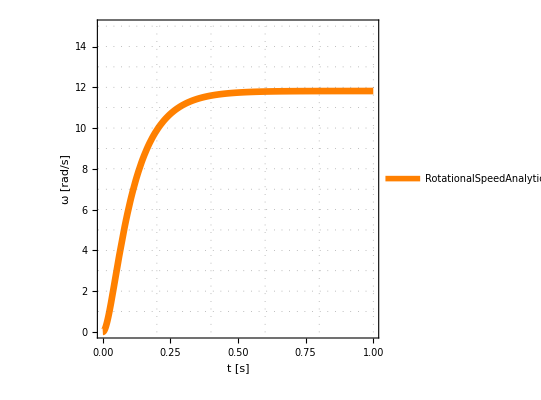

```mathematica
RotationalSpeedAnalyticPlot = Plot[RotationalSpeedAnalytic[t,12,0,0,0],{t,0,1},PlotRange->{{0,1},{0,15}},FrameLabel->{"t [s]","ω [rad/s]"},LabelStyle->Directive[FontSize->16],PlotTheme->"Detailed",Frame->True,GridLines->{Table[i,{i,0.2,1,0.2}],Table[i,{i,1,15}]},GridLinesStyle->Directive[Dotted, Gray],AspectRatio->1,PlotStyle->{Thickness[0.012],Orange}]
```

```mathematica
Max[RotationalAccelerationAnalytic/.t->Table[i,{i,0,1,0.001}]]
```

77.5598

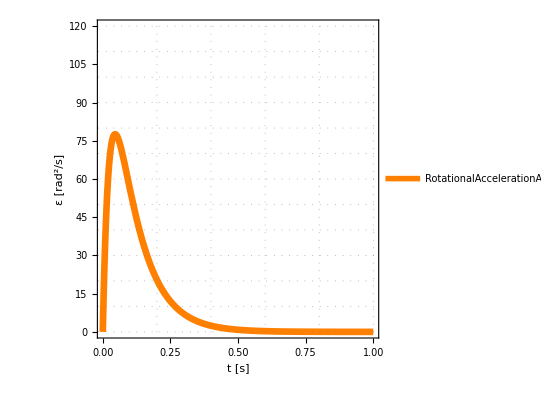

```mathematica
RotationalAccelerationAnalyticPlot = Plot[RotationalAccelerationAnalytic,{t,0,1},PlotRange->{{0,1},{0,120}},FrameLabel->{"t [s]","ε [rad^2/s]"},LabelStyle->Directive[FontSize->16],PlotTheme->"Detailed",Frame->True,GridLines->{Table[i,{i,0.2,1,0.2}],Table[i,{i,0,120,10}]},GridLinesStyle->Directive[Dotted, Gray],AspectRatio->1,PlotStyle->{Thickness[0.012],Orange}]
```

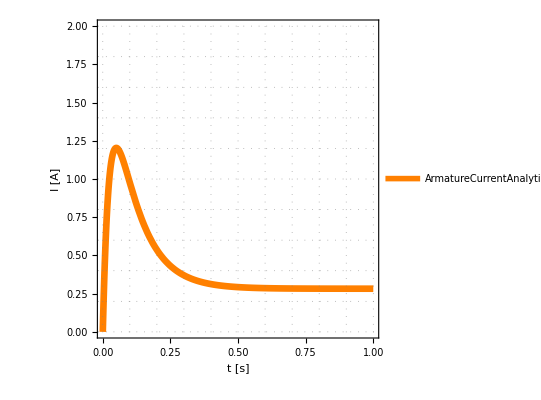

```mathematica
ArmatureCurrentAnalyticPlot = Plot[ArmatureCurrentAnalytic[t,12,0,0,0],{t,0,1},PlotRange->{{0,1},{0,2}},FrameLabel->{"t [s]","I [A]"},LabelStyle->Directive[FontSize->16],PlotTheme->"Detailed",Frame->True,GridLines->{Table[i,{i,0,1,0.1}],Table[i,{i,0,2,0.2}]},GridLinesStyle->Directive[Dotted, Gray],AspectRatio->1,PlotStyle->{Thickness[0.012],Orange}]
```

Analytic solution simplified

### Model parameters (estimated with MATLAB)

```mathematica
L=0;V=12;TL=0;Clear[x];Clear[y];
```

### Model equations (x→ω[rad/s], y→i[A])

```mathematica
MomentEquation = θ x'[t] +b x[t] == k y[t]-TL;
KirchoffEquation = L y'[t]+R y[t] ==V-k x[t];
```

```mathematica
CombinedEquation = MomentEquation/.Solve[KirchoffEquation,y[t]][[1]]//Simplify;
```

```mathematica
solution = DSolve[{CombinedEquation,x[0]==ω0},x[t],t];
```

```mathematica
solution = DSolve[{CombinedEquation,x[0]==0},x[t],t];
```

```mathematica
RotationalSpeedAnalyticSimple = x[t]/.solution[[1]]//Simplify;
```

```mathematica
RotationalSpeedAnalyticSimplePlot = Plot[RotationalSpeedAnalyticSimple,{t,0,1},PlotRange->{{0,1},{0,15}},FrameLabel->{"t [s]","ω [rad/s]"},LabelStyle->Directive[FontSize->16],PlotTheme->"Detailed",Frame->True,GridLines->{Table[i,{i,0.2,1,0.2}],Table[i,{i,1,15}]},GridLinesStyle->Directive[Dotted, Gray],AspectRatio->1,PlotStyle->{Thickness[0.012],Orange}];
```

```mathematica
RotationalAccelerationAnalyticSimple=D[RotationalSpeedAnalyticSimple,t];
```

```mathematica
RotationalAccelerationAnalyticSimplePlot = Plot[RotationalAccelerationAnalyticSimple,{t,0,1},PlotRange->{{0,1},{0,120}},FrameLabel->{"t [s]","ε [rad^2/s]"},LabelStyle->Directive[FontSize->16],PlotTheme->"Detailed",Frame->True,GridLines->{Table[i,{i,0.2,1,0.2}],Table[i,{i,0,120,10}]},GridLinesStyle->Directive[Dotted, Gray],AspectRatio->1,PlotStyle->{Thickness[0.012],Orange}];
```

```mathematica
ArmatureCurrentAnalyticSimple = y[t]/.Solve[KirchoffEquation,y[t]][[1]]/.solution[[1]]//Simplify;
```

```mathematica
ArmatureCurrentAnalyticSimplePlot = Plot[ArmatureCurrentAnalyticSimple,{t,0,1},PlotRange->{{0,1},{0,2}},FrameLabel->{"t [s]","I [A]"},LabelStyle->Directive[FontSize->16],PlotTheme->"Detailed",Frame->True,GridLines->{Table[i,{i,0,1,0.1}],Table[i,{i,0,2,0.2}]},GridLinesStyle->Directive[Dotted, Gray],AspectRatio->1,PlotStyle->{Thickness[0.012],Orange}];
```

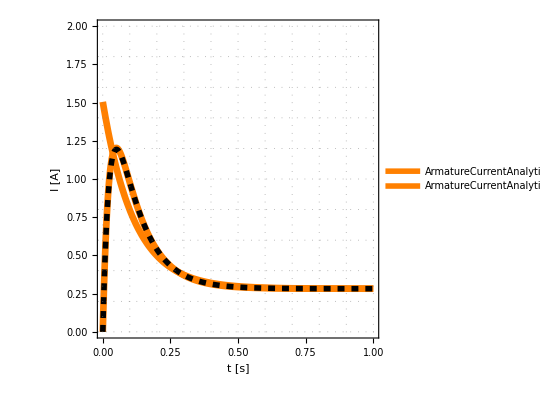

```mathematica
Show[ArmatureCurrentAnalyticSimplePlot,ArmatureCurrentAnalyticPlot,ArmatureCurrentNumeric]
```

```mathematica
ArmatureCurrentAnalyticSimple
```

0.282436+1.22209 ⅇ^(-8.6799 t)

```mathematica
ArmatureCurrentAnalytic[t,12,0,0,0]
```

0.282436-2.44311 ⅇ^(-39.1316 t)+2.16067 ⅇ^(-10.6896 t)

```mathematica
Integrate[ArmatureCurrentAnalytic[t,12,0,0,0],{t,0,1}]
```

0.422127

```mathematica
Integrate[ArmatureCurrentAnalyticSimple,{t,0,1}]
```

0.423208

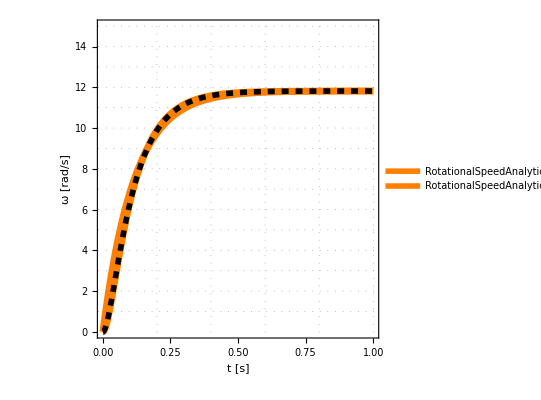

```mathematica
Show[RotationalSpeedAnalyticSimplePlot,RotationalSpeedAnalyticPlot,RotationalSpeedNumeric]
```

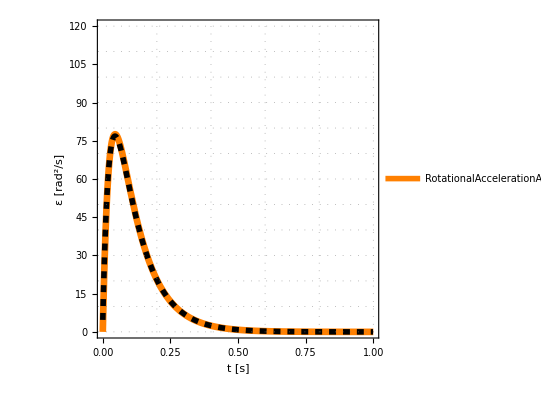

```mathematica
Show[RotationalAccelerationAnalyticPlot,RotationalAccelerationNumeric]
```

```mathematica
TorqueAnalytic = k y[t]/.Solve[KirchoffEquation,y[t]][[1]]/.solution[[1]]//Simplify
```

0.232974+1.00807 ⅇ^(-8.6799 t)

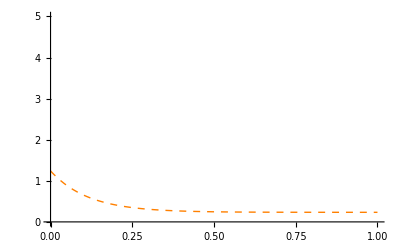

```mathematica
TorqueAnalyticPlot = Plot[TorqueAnalytic,{t,0,1},PlotRange->{0,5},PlotStyle->{Dashed,Orange,Thick}]
```

Numerical solutions

```mathematica
c1=0; 
c2=0; (*intitial values*)
t0=0; (*intitial time*)
Te=1;  (*end of time*)
h=0.001; (*stepsize *)
n=(Te-t0)/h; (*number of steps*)
V=12;TL=0;
θ=0.012099670934420;
b=0.019715497097366;
k=0.824871094407238;
R=7.975905973570620;
L=0.165503732732700;
```

```mathematica
f[t_,x_,y_]:=({{-b/θ, k/θ}, {-k/L, -R/L}}).{x,y}+({{-TL/θ}, {V/L}})//Flatten
```

#### Implicit Euler method (2^ndorder system)

```mathematica
Fx=AA-A-h f[tt,AA,BB][[1]];
Fy=BB-B-h f[tt,AA,BB][[2]];
F[tt_,AA_,BB_,t_,A_,B_]={Fx,Fy};
%//MatrixForm
```

(-A+AA-0.001 (0.-1.62942 AA+68.173 BB)
-B-0.001 (72.5059-4.984 AA-48.1917 BB)+BB)

```mathematica
J[AA_,BB_]=Grad[F[tt,AA,BB,t,A,B],{AA,BB}];
%//MatrixForm;
```

```mathematica
T=Table[t0+h i,{i,0,n}];  (*gridpoints: time*)
Y=Table[0,{i,1,2},{j,1,n+1}];  (*gridpoints: x,y*) 
Epsilon=Table[0,{i,1,n}];
Y[[All,1]]={c1,c2}; (*gridpoints: x,y*)
i=1;
For[i=1,i≤n,i++,                      (*external cycle: loading of Y[x,y]*)
Y[[All,i+1]]=Y[[All,i]];  (*0^th step: the previous value*)
For[j=1,j≤3,j++,                    (*internal cycle: Newton iteration*)
Y[[All,i+1]]=
	Y[[All,i+1]]-Inverse@J[Y[[1,i+1]],Y[[2,i+1]]]
								.
							F[T[[i+1]],Y[[1,i+1]],Y[[2,i+1]],T[[i]],Y[[1,i]],Y[[2,i]]]; (*x = x - J^-1(x).F(x)*)
];
Epsilon[[i]]=(Y[[1,i+1]]-Y[[1,i]])/h;
]
Y//MatrixForm;
Y[[All,n+1]]
plotIE=ListPlot[Table[{Y[[1,i]],Y[[2,i]]},{i,1,n+1}],PlotRange->{{0,15},{0,2}},Mesh->Full, Joined->True,FrameLabel->{"ω [rad/s]","I [A]"},LabelStyle->Directive[FontSize->16],PlotTheme->"Monochrome",Frame->True,GridLines->{Table[i,{i,1,15}],Table[i,{i,0,2,0.2}]},GridLinesStyle->Directive[Dotted, Gray],AspectRatio->1,PlotStyle->{Thickness[0.005],Black},PlotLegends->Automatic];
```

{11.8164,0.282488}

```mathematica
Epsilon[[All]];
```

```mathematica
RotationalSpeedNumeric=ListLinePlot[Table[{T[[i]],Y[[1,i]]},{i,1,n+1,1}],PlotRange->{{0,1},{0,15}},FrameLabel->{"t [s]","ω [rad/s]"},LabelStyle->Directive[FontSize->16],PlotTheme->"Detailed",Frame->True,GridLines->{Table[i,{i,0.1,1,0.1}],Table[i,{i,1,15}]},GridLinesStyle->Directive[Dotted, Gray],AspectRatio->1,PlotStyle->{Thickness[0.01],Black,Dashed}];
```

```mathematica
RotationalAccelerationNumeric=ListLinePlot[Table[{T[[i]],Epsilon[[i]]},{i,1,n,1}],PlotRange->{{0,1},{0,120}},FrameLabel->{"t [s]","ϵ [rad/s^2]"},LabelStyle->Directive[FontSize->16],PlotTheme->"Detailed",Frame->True,GridLines->{Table[i,{i,0.1,1,0.1}],Table[i,{i,0,100,10}]},GridLinesStyle->Directive[Dotted, Gray],AspectRatio->1,PlotStyle->{Thickness[0.01],Black,Dashed}];
```

```mathematica
ArmatureCurrentNumeric=ListLinePlot[Table[{T[[i]],Y[[2,i]]},{i,1,n+1,1}],PlotRange->{{0,1},{0,2}},FrameLabel->{"t [s]","I [A]"},LabelStyle->Directive[FontSize->16],PlotTheme->"Detailed",Frame->True,GridLines->{Table[i,{i,0,1,0.1}],Table[i,{i,0,2,0.2}]},GridLinesStyle->Directive[Dotted, Gray],AspectRatio->1,PlotStyle->{Thickness[0.01],Black,Dashed}];
```